## 1.

```mathematica
ut[v_,w_]:=u[x,y] + pdx (v - x) + pdy (w - y) + pdxx (v - x)^2/(2!)+pdxy (v-x)(w-y) + pdyy (v -y)^2/(2!)+pdxxx (v-x)^3/(3!)+pdxxy ((v-x)^2(w-y))/(2!)+pdxyy ((v-x)(w-y)^2)/(2!)+pdyyy (w-y)^3/(3!)+pdxxxx (v-x)^4/(4!)+pdxxxy ((v-x)^3(w-y))/(3!)+pdxxyy ((v-x)^2(w-y)^2)/(2!*2!)+pdxyyy ((v-x)(w-y)^3)/(3!)+pdyyyy (w-y)^4/(4!);
```

```mathematica
ut[x+h,y+h]-ut[x-h,y+h]-ut[x+h,y-h] +ut[x-h,y-h]
```

## 2.

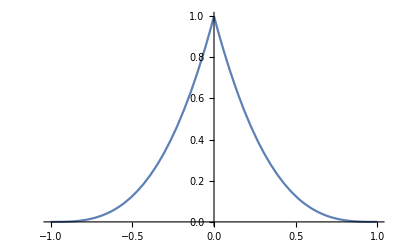

```mathematica
s[x_]:=Piecewise[{{(x + 1)^3, -1≤x≤0}, {(1-x)^3, 0≤x≤1}}]
Plot[s[x],{x,-1,1}]
```

## 4.

```mathematica
Roots[t^2-4t+2==0,t]
```

t==2-√2||t==2+√2

```mathematica
(2 + √2)/4*1/(3 - √2)+(2 - √2)/4*1/(3 + √2)//N
```

0.571429

```mathematica
NumberForm[0.5714285714285715,16]
```

0.5714285714285715

```mathematica
0.596347361-0.5714285714
```

0.0249188

```mathematica
0.024918789599999935
```

```mathematica
f[t_]:=1/(t+1)
```

```mathematica
D[f[t],{t,4}]
```

24/(1+t)^5

```mathematica
∫_0^∞ (t^2-4t+2)^2 ⅇ^-t ⅆt
```

4

```mathematica
(t^2-4t+2)^2//Expand
```

4-16 t+20 t^2-8 t^3+t^4

```mathematica
(4/0.024918789599999935)^(1/5)-1
```

1.76126

```mathematica
NumberForm[1.7612555998372623,16]
```

1.761255599837262

```mathematica
f''''[t]
```

24/(1+t)^5

## 5.

```mathematica
∫ⅇ^-x xⅆx
```

ⅇ^-x (-1-x)

```mathematica
∫_0^∞ ⅇ^-x xⅆx
```

1

```mathematica
∫ⅇ^-x x^2 ⅆx
```

ⅇ^-x (-2-2 x-x^2)

```mathematica
∫_0^∞ ⅇ^-x x^2 ⅆx
```

2

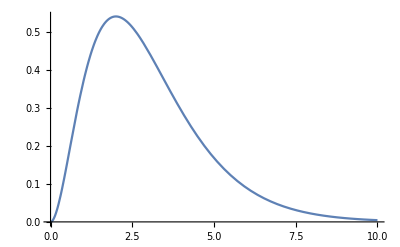

```mathematica
Plot[ⅇ^-x x^2,{x,0,10}]
```

```mathematica
p[x_]:=f[0] + (f[2]-f[0])/2 x + (((f[2]-f[0])/2-f'[2])/2)x(x-2)
```

```mathematica
∫_0^∞ ⅇ^-x p[x]ⅆx
```

1/2 (f[0]+f[2])

```mathematica
(x-2)^2 x//Expand
```

4 x-4 x^2+x^3

```mathematica
∫_0^∞ x(x-2)^2 ⅇ^-x ⅆx
```

2

## 6.

```mathematica
∫_1^2 ⅇ^x/x ⅆx//N
```

3.05912

```mathematica
NumberForm[3.059116539645953,16]
```

3.059116539645953